```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
(*Import leads *)
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,7,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{1}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
(*Or Generate leads using recursive algorithm*)
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

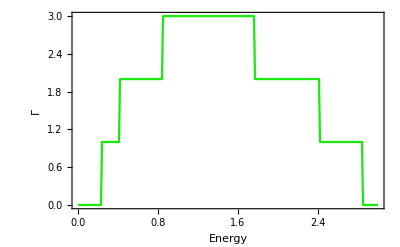

```mathematica
ListLinePlot[ParallelTable[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}],Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}]
```

```mathematica
list[num_,m_]:=Transpose[Join[{Range[1,100]},{RandomSample[Join[Table[0,100-num],Table[RandomInteger[{1,2*m}],num]]]}]]
```

```mathematica
dist=Table[list[50,7],5000]
```

{{{1,0},{2,0},{3,6},{4,0},{5,0},{6,7},{7,8},{8,0},{9,4},{10,2},{11,13},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},66,{84,1},{85,4},{86,0},{87,0},{88,0},{89,0},{90,0},{91,4},{92,0},{93,13},{94,0},{95,0},{96,9},{97,0},{98,0},{99,12},{100,0}},4998,{1}}
 |  |  |  |

```mathematica
CAvg[ω_,δ_,t_,ϵ_,ϵ1_,number_,size_]:=CAvg[ω,δ,t,ϵ,ϵ1,number,size]= Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{},
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-Inverse[Module[{κ=β[ω,δ,t,ϵ],n= dist[[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]].ConjugateTranspose[Tin].J.Tin].Inverse[Module[{κ=β[ω,δ,t,ϵ],n= dist[[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]],{loc1,1,size}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
CAvg[1,0.0001,1,0,0.5,504,100]
```

1.39351

```mathematica
Table[{ω,Mean[ParallelTable[CAvg[ω,0.0001,1,0,0.5,number,100],{number,5000}]]},{ω,Range[0,1.5,0.01]}]
```